```mathematica
cols=Short[ColorData[109,"ColorList"],4];
col1=cols[[1,8]]
col2=cols⟦1,9⟧
col3=cols[[1,10]]
col4=cols[[1,7]]
col5=cols⟦1,5⟧
col6=cols⟦1,14⟧
```

RGBColor[1., 0.325204, 0.406504]

RGBColor[0., 0.786874, 0.739379]

RGBColor[1., 0.520437, 0.]

RGBColor[0.238758, 0.610466, 1.]

RGBColor[0.893126, 0.4, 0.767184]

RGBColor[0, 0.7226017980018511, 0.9321946059944466]

```mathematica
Orange
orange=Blend[{Orange,Red},0.2]
Blue
blue=Blend[{Blue,Black},0.2]
```

RGBColor[1, 0.5, 0]

RGBColor[1., 0.4, 0.]

RGBColor[0, 0, 1]

RGBColor[0., 0., 0.8]

```mathematica
(*---------------Funtions for normal---------------*)
δ[p_,q_]:=Subscript[δ, min]+(Subscript[δ, 0]-Subscript[δ, min])*Exp[-(p-q)^2/(2*Subscript[k, 1]^2)];
ρ[p_]:=Subscript[ρ, min]+(Subscript[ρ, 0]-Subscript[ρ, min])*Exp[-p^2/(2*Subscript[k, 2]^2)];
μ[q_]:=Subscript[μ, min]+(Subscript[μ, 0]-Subscript[μ, min])*Exp[-q^2/(2*Subscript[k, 3]^2)];
G1[ϕ1_,p_,q1_,q2_,u_,v1_,v2_]:=ρ[ϕ1]*(1-u/κ)*(u/τ-1)-(δ[ϕ1,q1]*v1)/(1+δ[ϕ1,q1]*γ*u)-(δ[ϕ1,q2]*v2)/(1+δ[ϕ1,q2]*γ*u);
G21[ϕ21_,p_,q1_,q2_,u_,v1_,v2_]:=(α*δ[p,ϕ21]*u)/(1+δ[p,ϕ21]*γ*u)-μ[ϕ21];
G22[ϕ22_,p_,q1_,q2_,u_,v1_,v2_]:=(α*δ[p,ϕ22]*u)/(1+δ[p,ϕ22]*γ*u)-μ[ϕ22];
G11[p_,q1_,q2_,u_,v1_,v2_]:=D[G1[ϕ1,p,q1,q2,u,v1,v2],{ϕ1,1} ] /.ϕ1->p;
G212[p_,q1_,q2_,u_,v1_,v2_]:=D[G21[ϕ21,p,q1,q2,u,v1,v2],{ϕ21,1} ] /.ϕ21->q1;
G222[p_,q1_,q2_,u_,v1_,v2_]:=D[G22[ϕ22,p,q1,q2,u,v1,v2],{ϕ22,1} ] /.ϕ22->q2;
```

```mathematica
Subscript[ρ, 0]=0.75;Subscript[ρ, min]=0.25;κ=35;Subscript[δ, 0]=0.15;Subscript[δ, min]=0.05;γ=0.1;α=0.7;Subscript[μ, 0]=2.0;Subscript[μ, min]=1.0;Subscript[k, 1]=1.0;Subscript[k, 2]=1.0;Subscript[k, 3]=1.0;f=0.5;τ=1;
(*---------------------------------numetrical solution allee normal------------------------------------*)
sol2=NDSolve[{u'[t]==u[t]*G1[p[t],p[t],q1[t],q2[t],u[t],v1[t],v2[t]],p'[t]==f*G11[p[t],q1[t],q2[t],u[t],v1[t],v2[t]],v1'[t]==v1[t]*G21[q1[t],p[t],q1[t],q2[t],u[t],v1[t],v2[t]],q1'[t]==f*G212[p[t],q1[t],q2[t],u[t],v1[t],v2[t]],v2'[t]==v2[t]*G22[q2[t],p[t],q1[t],q2[t],u[t],v1[t],v2[t]],q2'[t]==f*G222[p[t],q1[t],q2[t],u[t],v1[t],v2[t]],u[0]==3,p[0]==2,v1[0]==3,q1[0]==-2,v2[0]==3,q2[0]==-2.1},{u,p, v1,q1,v2,q2},{t,0,20000},AccuracyGoal->8,PrecisionGoal->6,MaxSteps->10^6];
```

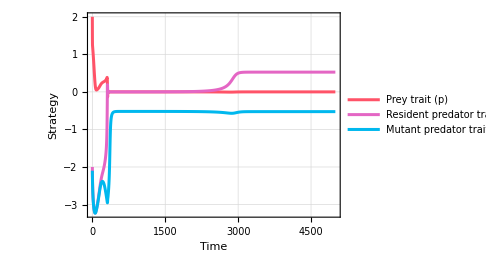

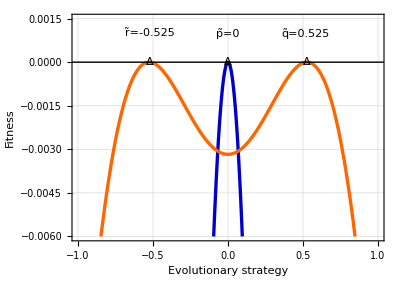

```mathematica
(*---fig 7A:Strategy dynamics---*)
B1=Plot[Evaluate[{p[t],q1[t],q2[t]}/. sol2],{t,0,5000},PlotRange->{All,All},PlotLegends->Placed[{"Prey trait (p)","Resident predator trait (q)","Mutant predator trait (r)"},{0.64,0.3}],LabelStyle->{FontSize->16},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{"Time","Strategy"},PlotStyle->{{col1,Thickness[0.006]},{col5,Thickness[0.006]},{col6,Thickness[0.006]}},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.5],Dotted,Thickness[0.002]],AspectRatio->1.5/2.1,ImageSize->Medium]

(*---fig 7B:Fitness landscape---*)
i=Plot[{Evaluate[G1[ϕ,p[9000]/.sol2[[1]],q1[9000]/.sol2[[1]],q2[9000]/.sol2[[1]],u[9000]/.sol2[[1]],v1[9000]/.sol2[[1]],v2[9000]/.sol2[[1]]]],Evaluate[G21[ϕ,p[9000]/.sol2[[1]],q1[9000]/.sol2[[1]],q2[9000]/.sol2[[1]],u[9000]/.sol2[[1]],v1[9000]/.sol2[[1]],v2[9000]/.sol2[[1]]]]},{ϕ,-2,2},PlotRange->{{-1,1},{-0.006,0.0015}},PlotStyle->{{blue,Thickness[0.006]},{orange,Thickness[0.006]}},Axes->False,FrameLabel->{"Evolutionary strategy","Fitness"},LabelStyle->{FontSize->16},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],AspectRatio->1.5/2.1,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.5],Dotted,Thickness[0.002]],ImageSize->400,Epilog->{Style[Text["Δ",{0,0}],FontSize->18,Bold],Style[Text["Δ",{0.525,0}],FontSize->18,Bold],Style[Text["Δ",{-0.525,0}],FontSize->18,Bold],Style[Text["q̃=0.525",{0.52,0.001}],FontSize->18,Background->White],Style[Text["r̃=-0.525",{-0.52,0.001}],FontSize->18,Background->White],Style[Text["p̃=0",{0,0.001}],FontSize->18,Background->White]}];

(*---Additional graphics---*)
j=Plot[x=0,{x,-5,5},PlotStyle->{GrayLevel[0],Thick}];
(*k1=Graphics[{Orange,PointSize[0.025],Point[{0.525,0}]}];
k2=Graphics[{Orange,PointSize[0.025],Point[{-0.525,0}]}];
k3=Graphics[{Orange,PointSize[0.025],Point[{0,0}]}];*)
C1=Show[i,j(*,k1,k2,k3*)]
```

```mathematica
g=Grid[{{Style["A: Trait dynamics",20],Style["B: Fitness at (u^(**),v^(**),p̃,q̃,r̃)",20]},{B1,C1}},Alignment->Center]
```

A: Trait dynamics | B: Fitness at (u^(**),v^(**),p̃,q̃,r̃)
-Graphics- | -Graphics-

```mathematica
Export[SystemDialogInput["FileSave","ebp1.pdf"],g,ImageResolution->350,"CompressionLevel"->0]
```

C:\Users\SANTANA\Dropbox\SANTANA\P7_G function\Mondal_allee effect\ebp1.pdf